```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={11159,11166,11277,11305,11363,11409,11412}];
(*2015:{10119,10124,10189,10246,10281,10345,10386,10420,10497,10541}
2016:{11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448}*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=1;binw=10;
my=Table[Table[0,{k,1,runn}],{l,1,18}];
mx=Table[Table[0,{k,1,runn}],{l,1,18}];
mx1=Table[Table[0,{k,1,runn}],{l,1,18}];
mx2=Table[Table[0,{k,1,runn}],{l,1,18}];
dmx=Table[Table[0,{k,1,runn}],{l,1,18}];
tm=Table[0,{k,1,runn}];
ptdat=Table[0,{l,1,18}];
chnum={1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {11159,11166,11277,11305,11363,11409,11412}

#Runs in the list: 7

```mathematica
For[runi=1,runi≤runn,runi++,data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
tm[[runi]]=DateObject[ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2][[25]][[1]]];
Print["Run #",runNum[[runi]]];
Print["Size of event list in Cycle: ",dimdata=Dimensions[data][[1]]];
Print["------------------------"];
(*Loop For NANOSc channels*)
For[j=1,j≤18,j++,
ChNum=chnum[[j]];
(*Print["Run #",runNum[[runi]]," : ",ChNum];*)
histdata=HistogramList[Select[data[[1;;dimdata,{3,7}]],#[[1]]==ChNum&][[;;,2]],{histbeg,histlast,binw}];
(*histdata=HistogramList[data[[1;;dimdata,6]],{histbeg,histlast,binw}];*)
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=13.6*(histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[i]][[2]]=histdata[[2]][[i]];
];
my[[j]][[runi]]=Max[histdata[[2]]];
f=Interpolation[ptdat];
(*Print["QDC peak of #",runNum[[runi]]," : ",ChNum," = ",Quiet[mx[[j]][[runi]]=x/.FindRoot[f[x]==my[[j]][[runi]],{x,7000}]]];*)
Quiet[mx[[j]][[runi]]=x/.FindRoot[f[x]==my[[j]][[runi]],{x,7000}]];
mx1[[j]][[runi]]=Quiet[x/.FindRoot[f[x]==my[[j]][[runi]]/E,{x,mx[[j]][[runi]]-1250}]];
mx2[[j]][[runi]]=Quiet[x/.FindRoot[f[x]==my[[j]][[runi]]/E,{x,mx[[j]][[runi]]+1250}]];
dmx[[j]][[runi]]=Abs[mx2[[j]][[runi]]-mx1[[j]][[runi]]];
(*Print["1/e points: ",mx1[[j]][[runi]]," , ",mx2[[j]][[runi]]];
Print["QDC width of #",runNum[[runi]]," : ",ChNum," = ",dmx[[j]][[runi]]=Abs[mx2[[j]][[runi]]-mx1[[j]][[runi]]]];*)
(*Print["Number of events in run #",runNum[[runi]]," : ",ChNum," = ",Total[histdata[[2]]]];
Print["------------------------"];*)
];
Print["****************RUN DONE****************"]
];
runi--;
```

Run #11159

Size of event list in Cycle: 142603

------------------------

****************RUN DONE****************

Run #11166

Size of event list in Cycle: 155557

------------------------

****************RUN DONE****************

Run #11277

Size of event list in Cycle: 189591

------------------------

****************RUN DONE****************

Run #11305

Size of event list in Cycle: 194674

------------------------

****************RUN DONE****************

Run #11363

Size of event list in Cycle: 168206

------------------------

****************RUN DONE****************

Run #11409

Size of event list in Cycle: 199658

------------------------

****************RUN DONE****************

Run #11412

Size of event list in Cycle: 218012

------------------------

****************RUN DONE****************

```mathematica
realpt=Table[Table[{(AbsoluteTime[tm[[i]]]-AbsoluteTime[tm[[1]]])/(3600*24),{mx[[k]][[i]],dmx[[k]][[i]]/2}},{i,1,runn}],{k,1,18}];
Export["2016_QDC_Dist_UCN#_t_A.png",GraphicsGrid[ArrayReshape[Table[EDAListPlot[realpt[[k]],Joined->True,Frame->True,PlotRange->{{-1,126},{0,10000}},FrameLabel->{"Run # (Days)","Maxima of QDC (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLabel->StringJoin["Channel # ",ToString[k]],Filling->Axis,ImageSize->{500}],{k,1,9}],{3,3}],ImageSize->{1600}]]
Export["2016_QDC_Dist_UCN#_t_B.png",GraphicsGrid[ArrayReshape[Table[EDAListPlot[realpt[[k]],Joined->True,Frame->True,PlotRange->{{-1,126},{0,10000}},FrameLabel->{"Run # (Days)","Maxima of QDC (e.ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLabel->StringJoin["Channel # ",ToString[k+1]],Filling->Axis,ImageSize->{500}],{k,10,18}],{3,3}],ImageSize->{1600}]]
```

2016_QDC_Dist_UCN#_t_A.png

2016_QDC_Dist_UCN#_t_B.png

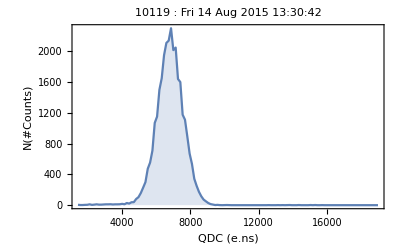

```mathematica
lineStyle={Thin,Red,Dashed};
line11=Line[{{mx1[[1]][[runi]],0},{mx1[[1]][[runi]],13000}}];
line12=Line[{{mx2[[1]][[runi]],0},{mx2[[1]][[runi]],13000}}];
line13=Line[{{0,my[[1]][[runi]]/E},{18000,my[[1]][[runi]]/E}}];
ListLinePlot[ptdat,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLabel->StringJoin[ToString[runNum[[runi]]]," : ",DateString[tm[[runi]]]],Filling->Axis,ImageSize->{1000}(*,Epilog->{{Directive[lineStyle],line11,line12,line13}}*)]
```

```mathematica
(AbsoluteTime[tm[[10]]]-AbsoluteTime[tm[[1]]])/(3600*24)
```

124.120435443877314815